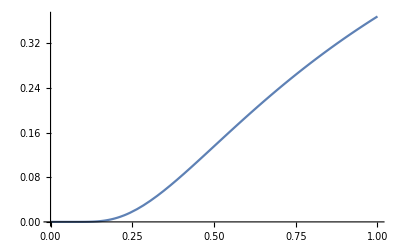

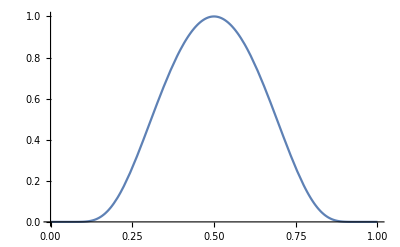

```mathematica
f[t_]=If[t≤0,0,If[t>0,Exp[-1/t]]];
g[t_]:=f[t] f[1-t]/(f[1/2])^2;
Plot[f[t],{t,0,1}]
Plot[g[t],{t,0,1}]
```